Autor: Krzysztof Barczak

# Metody numeryczne w technice

## (kierunek Matematyka)

## Projekt 9

Metoda odchyłek ważonych

Napisać procedurę realizującą metodę odchyłek ważonych dla równania:

u''(x)-3u'(x)=4x,   x∈(2,3),

z warunkami brzegowymi:

u(2)=0,
u(3)=0.

Przyjąć, że funkcje kształtu będą spełniały zadane warunki brzegowe.

a) Korzystając z napisanej procedury wyznaczyć metodą Galerkina rozwiązanie przybliżone przyjmując jako funkcje kształtu:

Φ_1(x)=(x-2)(x-3),   
Φ_2(x)=x(x-2)(x-3).

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązanie przybliżone. Policzyć także normę (w L^2) różnicy pomiędzy rozwiązaniem dokładnym i przybliżonym (wynik podać w postaci ułamka dziesiętnego).

b) Wykonać te same obliczenia dla trzech funkcji kształtu:

Φ_1(x)=(x-2)(x-3),   
Φ_2(x)=x(x-2)(x-3),   
Φ_3(x)=x^2(x-2)(x-3).

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązanie przybliżone. Policzyć także normę (w L^2) różnicy pomiędzy rozwiązaniem dokładnym i przybliżonym (wynik podać w postaci ułamka dziesiętnego).

## Rozwiązanie

### Kod procedury

Procedura realizuje metodę odchyłek ważonych przy założeniu, że funkcje kształtu spełniają zadane warunki brzegowe.

Rozważane jest równanie:
	A(T(x)) = B(x) dla x∈(a,b) oraz T(x) = φ(x) dla x∈{a,b}.
Wejście:
	operatorA - operator różniczkowy A;
	BB - funkcja B;
	Ω - przedział (a,b);
	φ - funkcja zadana na brzegu Γ1;
	Γ1 - brzeg;
	wagi - układ liniowo niezależnych funkcji wagowych;
	bazowe - funkcje kształtu;
	z - zmienna.
Wyjście:
	rozwiązanie przybliżone w postaci funkcji.

```mathematica
Clear[mow];
mow[operatorA_,BB_,Ω_,φ_,Γ1_,wagi_,bazowe_,z_Symbol]:=Module[{AA=operatorA,R0,R1,R2,w=wagi,n=Length[bazowe],T,uklad,rozwiazanie},

T[x_]:=Sum[p[i]*Function[bazowe[[i]]][x],{i,1,n}];
(*R0[x_]:=AA[x][T[x]]-BB[x];*)
R0[x_]=(AA[x][#]-BB[x])&;
(*R1[x_]:=T[x]-φ[x];*)
R1[x_]=(#-φ[x])&;
(*R2[x_]:=T'[x]-q[x];*)
R2[x_]=(D[#,x]-q[x])&;

(*uklad=Table[∫_Ω⟦1⟧^Ω⟦2⟧ (w⟦i⟧&)[x] R0[x][T[x]]ⅆx+∫_Γ1⟦1⟧^Γ1⟦2⟧ (wb1⟦i⟧&)[x] R1[x][T[x]]ⅆx+∫_Γ2⟦1⟧^Γ2⟦2⟧ (wb2⟦i⟧&)[x] R2[x][T[x]]ⅆx==0,{i,n}];*)
uklad=Table[∫_Ω⟦1⟧^Ω⟦2⟧ (w⟦i⟧&)[x] R0[x][T[x]]ⅆx==0,{i,n}];

rozwiazanie=Solve[uklad,Table[p[i],{i,n}]];
(*Print["rozwiazanie ",rozwiazanie];*)

Return[Sum[rozwiazanie[[1,i,2]]*Function[bazowe[[i]]][z],{i,1,n}]]
]
```

### Norma w L^p

```mathematica
normaLp[f_,p_,a_,b_]:=Module[{norma},
norma=(∫_a^b Abs[f[x]]^p ⅆx)^(1/p);
Return[norma]]
```

### Przykład 1.1 z wykładu

```mathematica
Clear[p,op,BB,Ω,φ,Γ1,wagi,bazowe,z];
op[t_]=(D[#,{t,2}]+#+t)&;
BB[x_]:=0;
Ω={0,1};
φ[x_]:=Piecewise[{{0,x==0},{0,x==1}}];
Γ1={0,1};
bazowe={x(x-1),x^2(x-1)};
wagi={1,x};
mow[op,BB,Ω,φ,Γ1,wagi,bazowe,z]
```

-122/649 (-1+x) x-10/59 (-1+x) x^2

### ad a)

```mathematica
Clear[op,BB,Ω,φ,Γ1,q,Γ2,wagi,bazowe,z,przyblizone,dokladne];
op[t_]=(D[#,{t,2}]-3D[#,t])&;
BB[x_]:=4x;
Ω={2,3};
φ[x_]:=Piecewise[{{0,x==2},{0,x==3}}];
Γ1={2,3};
bazowe={(x-2)(x-3),x(x-2)(x-3)};
wagi=bazowe;
```

```mathematica
przyblizone=mow[op,BB,Ω,φ,Γ1,wagi,bazowe,z]
```

-556/69 (-3+x) (-2+x)+340/69 (-3+x) (-2+x) x

```mathematica
dokladne=DSolve[{op[x][u[x]]==BB[x],u[Ω[[1]]]==φ[Ω[[1]]],u[Ω[[2]]]==φ[Ω[[2]]]},u[x],x][[1,1,2]]
```

-(2 (33 ⅇ^6-16 ⅇ^9-17 ⅇ^(3 x)-2 ⅇ^6 x+2 ⅇ^9 x-3 ⅇ^6 x^2+3 ⅇ^9 x^2))/(9 ⅇ^6 (-1+ⅇ^3))

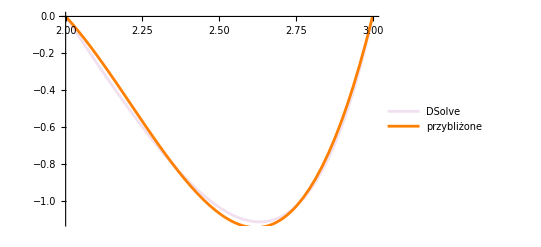

```mathematica
Show[Plot[dokladne,{x,Ω[[1]],Ω[[2]]},PlotLegends->{"DSolve"},PlotStyle->LightPurple],Plot[przyblizone,{x,Ω[[1]],Ω[[2]]},PlotLegends->{"przybliżone"},PlotStyle->Orange]]
```

```mathematica
Clear[f];
f[x_]:=przyblizone-dokladne;
normaLp[f,2,Ω[[1]],Ω[[2]]]
```

(17 √(2/7 (96973-31658 ⅇ^3+1339 ⅇ^6)))/(621 (-1+ⅇ^3))

```mathematica
%//N
```

0.0276032

### ad b)

```mathematica
Clear[op,BB,Ω,φ,Γ1,wagi,bazowe,z,przyblizone,dokladne];
op[t_]=(D[#,{t,2}]-3D[#,t])&;
BB[x_]:=4x;
Ω={2,3};
φ[x_]:=Piecewise[{{0,x==2},{0,x==3}}];
Γ1={2,3};
bazowe={(x-2)(x-3),x(x-2)(x-3),x^2(x-2)(x-3)};
wagi=bazowe;
```

```mathematica
przyblizone=mow[op,BB,Ω,φ,Γ1,wagi,bazowe,z]
```

43/3 (-3+x) (-2+x)-77/6 (-3+x) (-2+x) x+7/2 (-3+x) (-2+x) x^2

```mathematica
dokladne=DSolve[{op[x][u[x]]==BB[x],u[Ω[[1]]]==φ[Ω[[1]]],u[Ω[[2]]]==φ[Ω[[2]]]},u[x],x][[1,1,2]]
```

-(2 (33 ⅇ^6-16 ⅇ^9-17 ⅇ^(3 x)-2 ⅇ^6 x+2 ⅇ^9 x-3 ⅇ^6 x^2+3 ⅇ^9 x^2))/(9 ⅇ^6 (-1+ⅇ^3))

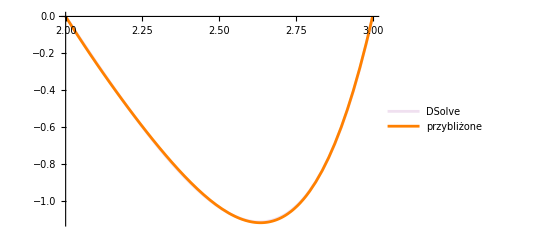

```mathematica
Show[Plot[dokladne,{x,Ω[[1]],Ω[[2]]},PlotLegends->{"DSolve"},PlotStyle->LightPurple],Plot[przyblizone,{x,Ω[[1]],Ω[[2]]},PlotLegends->{"przybliżone"},PlotStyle->Orange]]
```

```mathematica
Clear[f];
f[x_]:=przyblizone-dokladne;
normaLp[f,2,Ω[[1]],Ω[[2]]]
```

(√(1/30 (104991+35770 ⅇ^3-2041 ⅇ^6)))/(18 (-1+ⅇ^3))

```mathematica
%//N
```

0.00385029